## Relaciones Binarias

```mathematica
<<VilCretas`
```

```mathematica
(*------------------------------------------------------------------------*)
```

```mathematica
(* Calcular el Producto Cartesiano con VilCretas *)
```

```mathematica
PC[{a,b,c},{1,2,3}]
```

{{a,1},{a,2},{a,3},{b,1},{b,2},{b,3},{c,1},{c,2},{c,3}}

```mathematica
(*----------------------------------------------------------------------------*)
```

```mathematica
(* No se puede usar el comando PC porque aqui son intervalos y PC solo acepta conjuntos finitos *)
```

```mathematica
(* El producto cartesiano a la hora de graficarlo va ser un rectángulo *)
(* Si se pone el Infinity en alguno de los pares se interpreta como 100 o -100 *)
```

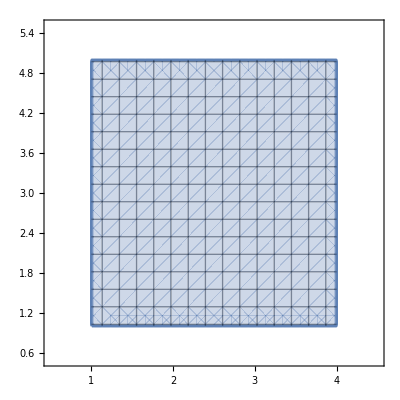

```mathematica
GraficaPC[{1,4},{1,5}]
```

```mathematica
(*-------------------------------------------------------------------------*)
```

```mathematica
(* Toda función es una relación binaria *)
```

```mathematica
(*---------------------------------------------------------------------------*)
```

```mathematica
(* Forma manual: *)
```

```mathematica
(* Para saber el rango y el dominio hay que excuir de los pares del subconjunto cuáles no cumplen con la condición que es que el mcd sea 1 *)

(* Para saber el dominio y el rango se ve A(en el caso del dominio) y B(en el caso del rango) y se compara con los pares del subconjunto para ver si HAY AL MENOS 1 que tiene ese número *)
```

```mathematica
(* Para 1 y para 3 se satisface que el conjunto resultante no será vacío *)
```

```mathematica
(* Con Mathematica: *)
```

```mathematica
(* Range da los núms impares de valor a valor, en este caso, de 1 a 7 incrementándose en 2 *)
```

```mathematica
A=Range[1,7,2]
```

{1,3,5,7}

```mathematica
B=Range[2,8,2]
```

{2,4,6,8}

```mathematica
PC[A,B]
```

{{1,2},{1,4},{1,6},{1,8},{3,2},{3,4},{3,6},{3,8},{5,2},{5,4},{5,6},{5,8},{7,2},{7,4},{7,6},{7,8}}

```mathematica
(* El único que no cumple con que el máx común divisor que da 1 es 3,6 *)
```

```mathematica
(* La relación sería distinta a vacía si el mcd es 3 o 1 *)
```

```mathematica
(* Resolver con mathematica: *)
(* RelBin: Relación Binaria *)
```

```mathematica
R=RelBin["GCD[a,b]==1",A,B]
```

{{1,2},{1,4},{1,6},{1,8},{3,2},{3,4},{3,8},{5,2},{5,4},{5,6},{5,8},{7,2},{7,4},{7,6},{7,8}}

```mathematica
DominioRelBin[R]
```

{1,3,5,7}

```mathematica
RangoRelBin[R]
```

{2,4,6,8}

```mathematica
(* Va mostrando desde 1 hasta 30, tomándolos como un mcm como condición, cuáles serían los conjuntos resultantes: *)
```

```mathematica
Table[i->RelBin["GCD[a,b]==i",A,B],{i,30}]
```

{1→{{1,2},{1,4},{1,6},{1,8},{3,2},{3,4},{3,8},{5,2},{5,4},{5,6},{5,8},{7,2},{7,4},{7,6},{7,8}},2→{},3→{{3,6}},4→{},5→{},6→{},7→{},8→{},9→{},10→{},11→{},12→{},13→{},14→{},15→{},16→{},17→{},18→{},19→{},20→{},21→{},22→{},23→{},24→{},25→{},26→{},27→{},28→{},29→{},30→{}}

```mathematica
(*------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(* A mano: *)
```

```mathematica
(* Con Mathematica: *)
```

```mathematica
A=Range[5]
```

{1,2,3,4,5}

```mathematica
(* RelBin solo acepta conjuntos finitos *)
```

```mathematica
(* Esto es un ejemplo de una relacion homogénea porque ambos conjuntos son iguales, A y A *)
```

```mathematica
R=RelBin["a>=b",A,A]
```

{{1,1},{2,1},{2,2},{3,1},{3,2},{3,3},{4,1},{4,2},{4,3},{4,4},{5,1},{5,2},{5,3},{5,4},{5,5}}

```mathematica
(* Cardinalidad o cantidad de pares ordenados: *)
```

```mathematica
Length[R]
```

15

```mathematica
(* Para graficarla debe ser finita, y los pares ordenados deben ser numéricos *)
```

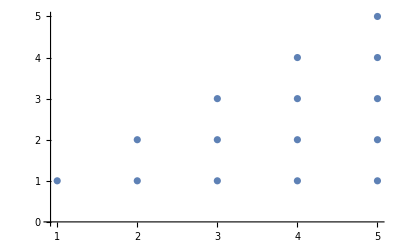

```mathematica
GraficaRelBinPares[R]
```

```mathematica
(* Cardinalidades : de 1 hasta 15 *)
```

```mathematica
list=Table[Length[RelBin["a>=b",Range[n],Range[n]]],{n,1,15}]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120}

```mathematica
(* Fórmula para averiguar cantidad de elementos de la relación binaria o cardinalidad el conjunto *)
```

```mathematica
(* O también resolviéndola con FindRRHL: *)
```

```mathematica
(* O también con: *)
```

```mathematica
FindSequenceFunction[list,n]
```

1/2 n (1+n)

```mathematica
(*----------------------------------------------------------------------------------------------*)
```

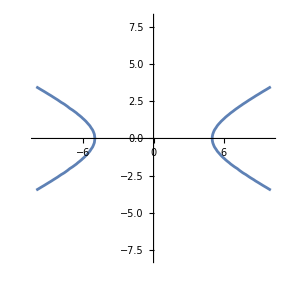

```mathematica
(* Esta es distinta porque al ser a y b núms reales, R no va ser finito *)
(* Se usa GraficaRelBin y se ve la grafica que da, de ahí se ve el dominio en x y el rango en y *)

GraficaRelBin["a^2/25-b^2/4==1",10,8,xmin->-10, ymin->-8]
```

```mathematica
(* Para saber si esos pares forman parte de R *)
```

```mathematica
L={{5 Sqrt[2],2 Sqrt[3]},{-5,0},{2 Sqrt[7],2/5 Sqrt[3]},{Sqrt[2],(6 Sqrt[3])/5},{-6,(2 Sqrt[11])/5},{5 Sqrt[3],-2 Sqrt[2]},{1/4,1/25},{7 Sqrt[7],-((2 Sqrt[318])/5)},{11/2,-(Sqrt[21]/5)},{-3,(2 Sqrt[34])/5}};
```

```mathematica
Table[ElementRelBinQ["a^2/25-b^2/4==1",punto,expalgebra->True],{punto,L}]
```

{False,True,True,False,True,True,False,True,True,False}

```mathematica
(*------------------------------------------------------------------------------------------------------*)
```

```mathematica
A=Range[1,99,2]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

```mathematica
(* Recordar: se pone el ; para que se cargue en R pero no se muestre *)
```

```mathematica
R=RelBin["b^3>=a",A,A];
```

```mathematica
(* no se pone exalgebra en ElementoRelBinQ porque no estamos poniendo una condicion o criterio, y esta definida sobre el conjunto de n reales*)
```

```mathematica
(*---------------------------------------------------------------------------------*)
```

```mathematica
(* Las relaciones binarias se pueden representar através de una matriz o un grafo *)
```

```mathematica
(*---------------------------------------------------------------------------------*)
```

```mathematica
-Graphics-
(* Ej 4.3 *)
-Graphics-
```

```mathematica
-Graphics--Graphics-
```

```mathematica
(* Con Mathematica: *)
```

```mathematica
(* Esta matriz no necesariamente será única *)
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
(*Ej 4.6: *)
```

```mathematica
A=Range[1,99,2]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

```mathematica
R=RelBin["b^3>=a",A,A];
MatrizRelBin[R,A,A];
```

```mathematica
(*---------------------------------------------------------------------------------------*)
```

```mathematica
(* Los grafos solo existen para las relaciones binarias homogéneas *)
```

```mathematica
(*----------------------------------------------------------------------------------------*)
```

```mathematica
(* Para el digrafo se van represantando los pares, haciendo una flecha dirigida de a hasta b, una flecha dirigida a el mismo número se llama lazo *)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
A=Range[5]
```

{1,2,3,4,5}

```mathematica
R=RelBin["a+b>=6",A,A]
```

{{1,5},{2,4},{2,5},{3,3},{3,4},{3,5},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}}

```mathematica
(*Hacer un digrafo, solo recibe A porque si A y B no son iguales, el grafo no existiria: *)
```

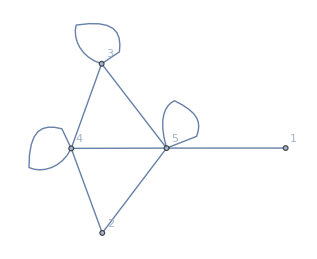

```mathematica
GrafoRelBin[R,A]
```

```mathematica
(* Este es un ejemplo de relación simétrica: aRb < = > bRa  porque a+b>=b < = > b+a>=b  *)
(* Como es simétrica mathematica no dibuja flechas, pero si no fuera siempre se dibuja con flechas *)
EdgeList[-Graphics-]
(* Pares ordenados: *)
```

{1<->5,2<->4,2<->5,3<->3,3<->4,3<->5,4<->4,4<->5,5<->5}

```mathematica
(*--------------------------------------------------------------------------------------------------*)
```

```mathematica
A=Range[2,100,2]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100}

```mathematica
(* Despejar k: *)
```

```mathematica
(* k= (ln a)/(ln b) = logb a *)
```

```mathematica
(* Usamos IntegerQ que es un comando que dice si lo que es pasado por parametro es entero o no, ej: *)
```

```mathematica
R=RelBin["IntegerQ[Log[b,a]]",A,A]
```

{{2,2},{4,2},{4,4},{6,6},{8,2},{8,8},{10,10},{12,12},{14,14},{16,2},{16,4},{16,16},{18,18},{20,20},{22,22},{24,24},{26,26},{28,28},{30,30},{32,2},{32,32},{34,34},{36,6},{36,36},{38,38},{40,40},{42,42},{44,44},{46,46},{48,48},{50,50},{52,52},{54,54},{56,56},{58,58},{60,60},{62,62},{64,2},{64,4},{64,8},{64,64},{66,66},{68,68},{70,70},{72,72},{74,74},{76,76},{78,78},{80,80},{82,82},{84,84},{86,86},{88,88},{90,90},{92,92},{94,94},{96,96},{98,98},{100,10},{100,100}}

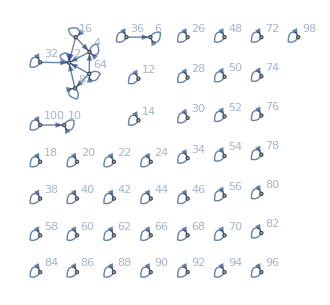

```mathematica
GrafoRelBin[R,A]
```

## Operaciones de Relaciones Binarias

```mathematica
-Graphics--Graphics-
```

```mathematica
(* Para el complemento: *)
```

```mathematica
(* El conjunto universal siempre es el Producto cartesiano *)
```

```mathematica
(*---------------------------------------------------------------------------*)
```

```mathematica
(* Recordar: los pares en mathematica son con llaves y no con parentesis redondos *)
```

```mathematica
(* Manualmente: *)
```

```mathematica
(* Hacer el complemento: *)
```

```mathematica
(* Con Mathematica: *)
```

```mathematica
A=Range[5]
```

{1,2,3,4,5}

```mathematica
(* Recordar que los pares en mathematica son con llaves y no con parentesis redondos *)
```

```mathematica
R1={{1,1},{2,1},{3,2},{3,3},{4,3}};
```

```mathematica
R2=RelBin["a-b==1",A,A]
```

{{2,1},{3,2},{4,3},{5,4}}

```mathematica
Union[R1,R2]
```

{{1,1},{2,1},{3,2},{3,3},{4,3},{5,4}}

```mathematica
Intersection[R1,R2]
```

{{2,1},{3,2},{4,3}}

```mathematica
(* Para el complementoooooooooo recordar que antes se hace PC del o los conjuntos originales *)
```

```mathematica
Complement[PC[A,A],R2]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,2},{2,3},{2,4},{2,5},{3,1},{3,3},{3,4},{3,5},{4,1},{4,2},{4,4},{4,5},{5,1},{5,2},{5,3},{5,5}}

```mathematica
(* Recordar: PC calcula el producto cartesiano *)
```

```mathematica
(* Todo se deja igual, solo se pondría en el Range 100 en vez de 5 *)
```

```mathematica
(*----------------------------------------------------------------------------*)
```

```mathematica
(* Ubicarse en cada número y ver cuáles son las aristas salientes: *)
```

```mathematica
R1={{1,1},{1,4},{1,5},{2,1},{2,4},{3,1},{4,2},{4,3},{4,4},{4,5}};
```

```mathematica
R2={{1,2},{1,4},{1,5},{2,2},{3,4},{4,1},{4,2},{4,3},{5,1},{5,3}};
```

```mathematica
(* Calcular unión e intersección: *)
```

```mathematica
Union[R1,R2]
```

{{1,1},{1,2},{1,4},{1,5},{2,1},{2,2},{2,4},{3,1},{3,4},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,3}}

```mathematica
Intersection[R1,R2]
```

{{1,4},{1,5},{4,2},{4,3}}

```mathematica
(* Calcular Complemento: *)
```

```mathematica
Complement[PC[Range[5],Range[5]],R1]
```

{{1,2},{1,3},{2,2},{2,3},{2,5},{3,2},{3,3},{3,4},{3,5},{4,1},{5,1},{5,2},{5,3},{5,4},{5,5}}

```mathematica
(* *-*-*- Imp: *-*-*- *)
```

## Inversa

```mathematica
(*------------------------------------------------------------------------*)
```

```mathematica
(* Si se pone solo Reverse[R] lo que hace es invertir el orden de los pares ordenados, el ultimo par seria el primero, etc *)
```

```mathematica
(* La inversa es darle la vuelta a los pares ordenados *)
```

```mathematica
(* El /@ es como usar Map, ambas instrucciones dan el mismo resultado: *)
```

## Composición

```mathematica
-Graphics-
-Graphics-
```

```mathematica
(*---------------------------------------------------------------------*)
```

```mathematica
(* Encontrar la Composición por definición, manualmente: *)
```

```mathematica
A=Range[4];
R1=RelBin["a>b",A,A];
R2=RelBin["a<b",A,A];
```

```mathematica
(* Nos fijamos en el b del cada par del segundo conjunto, y vemos cuáles pares del primer conjunto, el a coincide con ese b *)
(* En el primer caso sería 2, cuáles pares del primer conjunto empiezan con 2: solo 2,1 , entonces el par 1,1 se agrega a la composición *)

(* Siguiendo: *)
```

```mathematica
(* Con mathematica: *)
```

```mathematica
(* Función que calcula la Composición de dos conjuntos: *)
```

```mathematica
RelacionComposicion[R1_,R2_]:=Module[{Composicion={},i,j},For[i=1,i<=Length[R2],For[j=1,j<=Length[R1],If[R2[[i,2]]==R1[[j,1]],Composicion=Append[Composicion,{R2[[i,1]],R1[[j,2]]}]];j++];
i++];DeleteDuplicates[Composicion]]
RelacionComposicion[R1,R2]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

## Operaciones con Matrices booleanas

```mathematica
(* o : *)
```

```mathematica
(* y : *)
```

```mathematica
(* Producto booleano (no es conmutativo): *)
```

```mathematica
(* Se compara la primera fila con la primera columna hasta encontrar una pareja de unos, si se encuentra la entrada de la matriz en esa posicion es 1, si no se encuentra es 0 *)
```

```mathematica
CDFOperacionesMBooleanas[({{1, 0, 0, 0}, {1, 1, 0, 0}, {1, 0, 1, 1}, {0, 1, 0, 0}}),({{0, 0, 1, 0}, {0, 1, 0, 1}, {1, 0, 1, 0}, {1, 0, 1, 1}})]
```

```mathematica
(*-------------------------------------------------------------------------*)
```

```mathematica
(* Manualmente: *)
```

```mathematica
(* La composicion es lo mismo que el producto booleano, cambiando el orden de R1 y R2 *)
```

```mathematica
(* Producto booleano: *)
```

```mathematica
(* Comparar cada fila con cada columna y buscar parejas de 1, si no hay se pone un 0 como entrada *)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
(* Con Mathematica: *)
```

```mathematica
A={a,b,c,d};
```

```mathematica
MR1=({{1, 0, 0, 0}, {1, 1, 0, 0}, {1, 0, 1, 1}, {0, 1, 0, 0}});
MR2=({{0, 0, 1, 0}, {0, 1, 0, 1}, {1, 0, 1, 0}, {1, 0, 1, 1}});
```

```mathematica
(* Calcular Unión o calcular el o : *)
```

```mathematica
UnionBooleana[MR1,MR2]
```

(1 | 0 | 1 | 0
1 | 1 | 0 | 1
1 | 0 | 1 | 1
1 | 1 | 1 | 1)

```mathematica
(* Lo que devuelve eso de arriba, no es una matriz *)
(* Para cmabiar eso, se pone un lista-> True *)
UnionBooleana[MR1,MR2,lista->True]
```

{{1,0,1,0},{1,1,0,1},{1,0,1,1},{1,1,1,1}}

```mathematica
(* Ahora para calcular el resto de operaciones: *)
(* ***** Hay que poner lista -> True porque lo que devuelve UnionBooleana no es una matriz para mathematica ******** *)
```

## Unión:

```mathematica
RelBinMatriz[UnionBooleana[MR1,MR2,lista->True],A,A]
```

{{a,a},{a,c},{b,a},{b,b},{b,d},{c,a},{c,c},{c,d},{d,a},{d,b},{d,c},{d,d}}

## Intersección:

```mathematica
RelBinMatriz[InterseccionBooleana[MR1,MR2,lista->True],A,A]
```

{{b,b},{c,a},{c,c}}

## Complemento:

```mathematica
RelBinMatriz[ComplementoBooleano[MR1,lista->True],A,A]
```

{{a,b},{a,c},{a,d},{b,c},{b,d},{c,b},{d,a},{d,c},{d,d}}

## Inversa = Transpuesta:

```mathematica
(* La inversa es la Transpuesta: *)
(* Transpose devuelve lo que para mathematica es una matriz, no se pone lista -> True *)
```

```mathematica
RelBinMatriz[Transpose[MR1],A,A]
```

{{a,a},{a,b},{a,c},{b,b},{b,d},{c,c},{d,c}}

## Composición = Producto Booleano:

```mathematica
(* Hay que poner MR2 primeroooooooooooooo *)
```

```mathematica
RelBinMatriz[ProductoBooleano[MR2,MR1,lista->True],A,A]
```

{{a,a},{a,c},{a,d},{b,a},{b,b},{c,a},{c,c},{c,d},{d,a},{d,b},{d,c},{d,d}}

```mathematica
(* El % captura la salida de lo ultimo que fue ejecutado *)
```

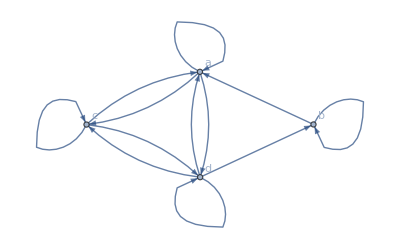

```mathematica
GrafoRelBin[%,A]
```

```mathematica
(* ------------------------------------------------------------------------------- *)
```

## Características de las Relaciones Binarias Homogéneas

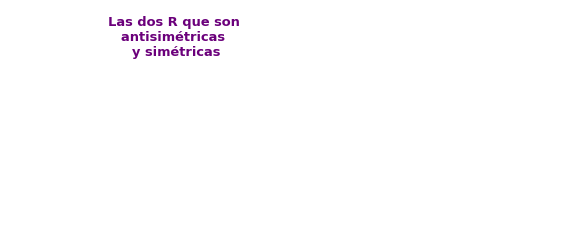
```mathematica
-Graphics--Graphics-
```

## Definición anterior con respecto a matrices

```mathematica
(* ---------------------------------------------------------------------------- *)
```

```mathematica
A=Range[4];
```

```mathematica
R1={{1,1},{1,2},{2,1},{2,2},{3,3},{3,4},{4,3},{4,4}};
```

```mathematica
MR1=MatrizRelBin[R1,A,A,table->False]
```

{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}}

Determinar si la matriz es reflexiva:

```mathematica
(* Si es reflexiva, porque la diagonal principal está formada por unos *)
```

```mathematica
(* El comando Diagonal, devuelve la diagonal principal de la matriz *)
```

```mathematica
MR1=MR1[[1]];
```

```mathematica
Diagonal[MR1]
```

{1,1,1,1}

```mathematica
(* Verificar si no hay ceros: *)
```

```mathematica
!MemberQ[Diagonal[MR1],0]
```

True

Determinar si la matriz es simétrica:

```mathematica
Transpose[MR1]==MR1
```

True

```mathematica
(*--------------------------------------------------------------------------------------------------*)
```

```mathematica
(* Este comando selecciona conforme al criterio que se le da: *)
```

```mathematica
Select[{1,2,3,4,5},#>3&]
```

{4,5}

```mathematica
(* Position: da la posicion del num que se le este dando *)
```

```mathematica
(* Da la posicion de los unos en la matriz MR1 *)
```

```mathematica
Position[MR1,1]
```

{{1,1},{1,2},{2,1},{2,2},{3,3},{3,4},{4,3},{4,4}}

Determinar si la matriz es anti simétrica:

```mathematica
(* Con esta instrucción, decimos que seleccione, de las posiciones que tengan 1 de la matriz, que no sean de la diagonal principal, o sea, que i != j *)
```

```mathematica
list=Select[Position[MR1,1],#[[1]]!=#[[2]]&];
```

```mathematica
(* Ahora, vamos a ver cuáles pares ordenados de esa lista, al darles vuelta siguen estando en esa misma lista *)
(* Recordar: que para la relación sea antisimétrica si tengo un 1 en l posicion i,j. En la posicion j,i de la matriz debería de haber un 0 *)
(* O sea, al ser 0, debería de ser conjunto vacío el resultado al buscar el el par dándole vuelta *)
```

```mathematica
(* El resultado da falso, porque ya se había probado que la relación era simétrica *)
```

```mathematica
Select[list,MemberQ[list,Reverse[#]]&]=={}
```

False

Determinar si la matriz es transitiva:

```mathematica
(* Aca, estamos calculando el prod booleano y luego la union, para asi al final comparar si el resultado es el mismo a MR1 *)
```

```mathematica
UnionBooleana[ProductoBooleano[MR1,MR1][[1]],MR1][[1]]==MR1
```

True

```mathematica
(* Como da verdadero significa que si es transitiva *)
```

```mathematica
(* ----- Ahora, como la relacion es reflexiva, simetrica y transitiva, significa que tenemos una relacion de equivalencia ---- *)
```

## Comando de VilCretas para verificar:

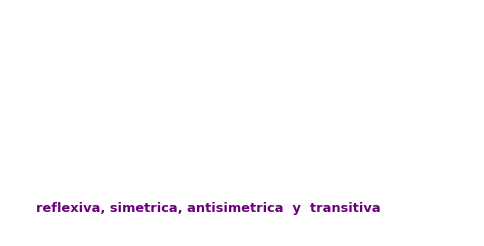
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Ahora, siguiendo con el resto de conjuntos: *)
```

```mathematica
R2={{1,3},{1,1},{3,1},{1,2},{3,3},{4,4}};
```

```mathematica
R3={};
```

```mathematica
R4={{1,2},{1,3},{3,1},{1,1},{3,3},{3,2},{1,4},{4,2},{3,4}};
```

```mathematica
(* Recordar: no necesariamente porque una relacion no sea simetrica significa que va a ser antisimetrica y viceversa *)
(* Pero si una relacion que no es la identidad o conjunto vacio es simetrica, ya no puede ser antisimetrica y viceversa *)
(*----------------------------------------*)
(* Clase presencial resolucion: *)
A=Range[4];
Subscript[R, 1]={{1,1},{1,2},{2,1},{2,2},{3,3},{3,4},{4,3},{4,4}};
Subscript[R, 2]={{1,3},{1,1},{3,1},{1,2},{3,3},{4,4}};
Subscript[R, 3]={};
Subscript[R, 4]={{1,2},{1,3},{3,1},{1,1},{3,3},{3,2},{1,4},{4,2},{3,4}};
```

```mathematica
Table[i->ClasificacionRelBin[Subscript[R, i],A],{i,4}]
```

{1→{True,True,False,True},2→{False,False,False,False},3→{False,True,True,True},4→{False,False,False,True}}

```mathematica
(*--------------------------------------------------------------------------------------------*)
```

```mathematica
(* La funcion o comando clasificacion RelBin puede usarse como demostracion siempre y cuando la relacion sea finitaaaaaaaaaa *)
```

```mathematica
(* La relacion seria de 100 x 100 o sea, 1000 pares ordenados *)
```

```mathematica
A=Range[100];
```

```mathematica
(* Relacion de congruencia: *)
```

```mathematica
(* Si x es congruente con: y mod k, esto significa que k divide a x-y*)
```

```mathematica
(* Al final lo que se obtiene significa que si a es congruente con r mod3 y b es congruente con r mod3, el residuo de esas divisiones tiene que ser igual,en este caso, igual al r que esta en rojo *)
(* -------- Si esos residuos son iguales entonces quiere decir que ese par esta en la relacion binaria ----------- *)
```

```mathematica
(* Resultado: *)
```

```mathematica
(* La relacion es de equivalencia porque es reflexiva, simetrica, y transitiva *)
```

```mathematica
(*-----------------------------------------------------------------------------------------------*)
```

```mathematica
(* Ejemplo 4.10: *)
```

```mathematica
(* Orden parcial: reflexiva, antisimetrica y transitiva *)
```

```mathematica
A=Range[2,100,2];
```

```mathematica
R=RelBin["IntegerQ[Log[b,a]]",A,A]
```

{{2,2},{4,2},{4,4},{6,6},{8,2},{8,8},{10,10},{12,12},{14,14},{16,2},{16,4},{16,16},{18,18},{20,20},{22,22},{24,24},{26,26},{28,28},{30,30},{32,2},{32,32},{34,34},{36,6},{36,36},{38,38},{40,40},{42,42},{44,44},{46,46},{48,48},{50,50},{52,52},{54,54},{56,56},{58,58},{60,60},{62,62},{64,2},{64,4},{64,8},{64,64},{66,66},{68,68},{70,70},{72,72},{74,74},{76,76},{78,78},{80,80},{82,82},{84,84},{86,86},{88,88},{90,90},{92,92},{94,94},{96,96},{98,98},{100,10},{100,100}}

```mathematica
ClasificacionRelBin[R,A]
```

{True,False,True,True}

```mathematica
(* Es reflexiva, antisimetrica y transitiva o sea es de orden parcial *)
```

```mathematica
(*----------------------------------------------------------------------------------*)
```

```mathematica
(* Como A es infinito se va a conjeturar que para algunos casos de A, se presenta la relacion de orden parcial *)
```

```mathematica
Table[A=Range[n];n->ClasificacionRelBin[RelBin["a<=b",A,A],A],{n,1,50}]
```

```mathematica
(* El num, es hasta donde esta evaluando el conjunto A, primero solo con 1, y asi sigue *)
```

{1→{True,True,True,True},2→{True,False,True,True},3→{True,False,True,True},4→{True,False,True,True},5→{True,False,True,True},6→{True,False,True,True},7→{True,False,True,True},8→{True,False,True,True},9→{True,False,True,True},10→{True,False,True,True},11→{True,False,True,True},12→{True,False,True,True},13→{True,False,True,True},14→{True,False,True,True},15→{True,False,True,True},16→{True,False,True,True},17→{True,False,True,True},18→{True,False,True,True},19→{True,False,True,True},20→{True,False,True,True},21→{True,False,True,True},22→{True,False,True,True},23→{True,False,True,True},24→{True,False,True,True},25→{True,False,True,True},26→{True,False,True,True},27→{True,False,True,True},28→{True,False,True,True},29→{True,False,True,True},30→{True,False,True,True},31→{True,False,True,True},32→{True,False,True,True},33→{True,False,True,True},34→{True,False,True,True},35→{True,False,True,True},36→{True,False,True,True},37→{True,False,True,True},38→{True,False,True,True},39→{True,False,True,True},40→{True,False,True,True},41→{True,False,True,True},42→{True,False,True,True},43→{True,False,True,True},44→{True,False,True,True},45→{True,False,True,True},46→{True,False,True,True},47→{True,False,True,True},48→{True,False,True,True},49→{True,False,True,True},50→{True,False,True,True}}

```mathematica
(* Con esto le pedimos que solo de como resultado donde están los verdaderos, en este caso sería la posición 1,3,4. Menos la primera que es la identidad *)
```

```mathematica
Table[A=Range[n];n->Position[ClasificacionRelBin[RelBin["a<=b",A,A],A],True],{n,20}]
```

{1→{{1},{2},{3},{4}},2→{{1},{3},{4}},3→{{1},{3},{4}},4→{{1},{3},{4}},5→{{1},{3},{4}},6→{{1},{3},{4}},7→{{1},{3},{4}},8→{{1},{3},{4}},9→{{1},{3},{4}},10→{{1},{3},{4}},11→{{1},{3},{4}},12→{{1},{3},{4}},13→{{1},{3},{4}},14→{{1},{3},{4}},15→{{1},{3},{4}},16→{{1},{3},{4}},17→{{1},{3},{4}},18→{{1},{3},{4}},19→{{1},{3},{4}},20→{{1},{3},{4}}}

```mathematica
(* ----------------------------------------------------------------------------------------- *)
```

## Particiones y Clases de Equivalencia

```mathematica
-Graphics--Graphics-
```

```mathematica
(* Una clase de equivalencia es formada por todos los elementos(b) que estan relacionados con a en el conjunto *)
```

```mathematica
(* [a] es como se denota una clase de equivalencia *)
```

```mathematica
(* Todas las clases de equivalencia, definidas sobre un conjunto R que es una relacion de equivalencia, van a hacer una particion en el conjunto original *)
```

```mathematica
(*---------------------------------------------------------------------------------*)
```

```mathematica
(* Demostrar que es una relacion de equivalencia: *)
```

```mathematica
(* Si la relacion no es de equivalencia, no tiene clases de equivalencia y no puede hacerse la particion *)
```

```mathematica
(* Particion: *)
```

```mathematica
(* Si dos elementos en una clase de equivalencia se relacionan, sus clases de equivalencia deben de ser iguales *)
```

```mathematica
(* Con Mathematica: *)
```

```mathematica
ClasesEquivalencia[R,A]
```

[1]={1,2,3}

[2]={1,2,3}

[3]={1,2,3}

[4]={4}

El conjunto de clases de equivalencia distintas es:

{{1,2,3},{4}}

```mathematica
(* Este comando solo devuelve la particion: *)
```

```mathematica
ParticionReEquivalencia[R,A]
```

{{1,2,3},{4}}

```mathematica
(* --------------- *)
A=Range[4];
R={{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3},{4,4}};
ClasificacionRelBin[R,A]
```

{True,True,False,True}

```mathematica
(*---------------------------------------------------------------------------------------*)
```

```mathematica
A={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321};
```

```mathematica
(* Como se quiere que tanto a como b sea palindromos, se pone && *)
```

```mathematica
R=RelBin["PalindromeQ[a] && PalindromeQ[b]",A,A];
(* Si la relacion no es de equivalencia, el comando no devuelve nada *)
RelacionEquivalenciaQ[R,A]
```

True

```mathematica
(* Ahora para saber las clases de equivalencia, por cada elemento de A debe de haber una clase de equivalencia *)
```

```mathematica
ClasesEquivalencia[R,A]
```

[101]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[252]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[313]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[404]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[575]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[646]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[717]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[898]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[939]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[1111]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[1551]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[2442]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[10301]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[10501]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[10601]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[11311]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[14941]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[34443]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[71617]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

[1234321]={101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}

El conjunto de clases de equivalencia distintas es:

{{101,252,313,404,575,646,717,898,939,1111,1551,2442,10301,10501,10601,11311,14941,34443,71617,1234321}}

```mathematica
(* La particion esta quedando igual que el conjunto A, porque los numeros son palindromos, o sea que AxA = R , no hay ningun par que no este en la relacion *)
```

```mathematica
(*---------------------------------------------------------------------------------------*)
```

```mathematica
(* Si yo tengo una particion, a partir de ella puedo generar una relacion de equivalencia *)
```

```mathematica
(*------------------------------------------------------------------------------------------*)
```

```mathematica
(* Piden todas las relaciones de equivalencia sobre un conjunto, o sea todas las posibles particiones *)
```

```mathematica
(* Posibles particiones a mano: *)
```

```mathematica
(* El teorema anterior dice que por cada particion se puede construir una relacion de equivalencia *)
(* Formar las relaciones de equivalencia: *)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
(* Las formo tomando cada conjunto y calculando el producto cruz del conjunto con él mismo *)
(* ******* Recordar: La identidad va ser no solamente simétrica y antisimétrica al mismo tiempo, sino que también va ser una relación de equivalencia y de orden parcial al mismo tiempo *)
```

```mathematica
(* Con Mathematica: *)
```

```mathematica
A=Range[3];
```

```mathematica
(* Paquete para usar SetPartitions: *)
```

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
(* Este comando devuelve todas las particiones del conjunto que se le pase *)
```

```mathematica
particiones=SetPartitions[A]
```

{{{1,2,3}},{{1},{2,3}},{{1,2},{3}},{{1,3},{2}},{{1},{2},{3}}}

```mathematica
(* El comando ReEquivalenciaParticion devuelve las relaciones de equivlencia, formadas por una particion y el conjunto al que pertenece *)
```

```mathematica
Table[i->ReEquivalenciaParticion[i,A],{i,particiones}]
```

{{{1,2,3}}→{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}},{{1},{2,3}}→{{1,1},{2,2},{2,3},{3,2},{3,3}},{{1,2},{3}}→{{1,1},{1,2},{2,1},{2,2},{3,3}},{{1,3},{2}}→{{1,1},{1,3},{2,2},{3,1},{3,3}},{{1},{2},{3}}→{{1,1},{2,2},{3,3}}}

```mathematica
(*----------------------------------------------------------------------*)
```

```mathematica
A={a,5,-20,b};
```

```mathematica
(* Este comando solo sirve si el conjunto es relativamente pequeño, sino el comando SetPartitions tardaría demasiado *)
```

```mathematica
particiones=SetPartitions[A]
```

{{{a,5,-20,b}},{{a},{5,-20,b}},{{a,5},{-20,b}},{{a,-20,b},{5}},{{a,5,-20},{b}},{{a,b},{5,-20}},{{a,5,b},{-20}},{{a,-20},{5,b}},{{a},{5},{-20,b}},{{a},{5,-20},{b}},{{a},{5,b},{-20}},{{a,5},{-20},{b}},{{a,-20},{5},{b}},{{a,b},{5},{-20}},{{a},{5},{-20},{b}}}

```mathematica
Table[i->ReEquivalenciaParticion[i,A],{i,particiones}]
Length[%]
```

{{{a,5,-20,b}}→{{-20,-20},{-20,5},{-20,a},{-20,b},{5,-20},{5,5},{5,a},{5,b},{a,-20},{a,5},{a,a},{a,b},{b,-20},{b,5},{b,a},{b,b}},{{a},{5,-20,b}}→{{-20,-20},{-20,5},{-20,b},{5,-20},{5,5},{5,b},{a,a},{b,-20},{b,5},{b,b}},{{a,5},{-20,b}}→{{-20,-20},{-20,b},{5,5},{5,a},{a,5},{a,a},{b,-20},{b,b}},{{a,-20,b},{5}}→{{-20,-20},{-20,a},{-20,b},{5,5},{a,-20},{a,a},{a,b},{b,-20},{b,a},{b,b}},{{a,5,-20},{b}}→{{-20,-20},{-20,5},{-20,a},{5,-20},{5,5},{5,a},{a,-20},{a,5},{a,a},{b,b}},{{a,b},{5,-20}}→{{-20,-20},{-20,5},{5,-20},{5,5},{a,a},{a,b},{b,a},{b,b}},{{a,5,b},{-20}}→{{-20,-20},{5,5},{5,a},{5,b},{a,5},{a,a},{a,b},{b,5},{b,a},{b,b}},{{a,-20},{5,b}}→{{-20,-20},{-20,a},{5,5},{5,b},{a,-20},{a,a},{b,5},{b,b}},{{a},{5},{-20,b}}→{{-20,-20},{-20,b},{5,5},{a,a},{b,-20},{b,b}},{{a},{5,-20},{b}}→{{-20,-20},{-20,5},{5,-20},{5,5},{a,a},{b,b}},{{a},{5,b},{-20}}→{{-20,-20},{5,5},{5,b},{a,a},{b,5},{b,b}},{{a,5},{-20},{b}}→{{-20,-20},{5,5},{5,a},{a,5},{a,a},{b,b}},{{a,-20},{5},{b}}→{{-20,-20},{-20,a},{5,5},{a,-20},{a,a},{b,b}},{{a,b},{5},{-20}}→{{-20,-20},{5,5},{a,a},{a,b},{b,a},{b,b}},{{a},{5},{-20},{b}}→{{-20,-20},{5,5},{a,a},{b,b}}}

```mathematica
(* Cantidad de relaciones de equivalencia formadas: *)
```

15

```mathematica
(* Este crecimiento es factorial *)
```

```mathematica
(* Intentar encontrar una sucesion para la cantidad de particiones de un conjunto *)
```

```mathematica
(* Cantidad de particiones distintas de 1 a 10 : *)
```

```mathematica
Table[A=Range[i];Length[SetPartitions[A]],{i,1,10}]
```

{1,2,5,15,52,203,877,4140,21147,115975}

```mathematica
(* Encontrar una formula, para saber la cantidad de relaciones de equivalencia *)
```

```mathematica
FindSequenceFunction[Table[A=Range[i];Length[SetPartitions[A]],{i,1,10}],n]
```

BellB[n]

```mathematica
(* El FindSequenceFunction busca un patrón con respecto a la relación o sequencia que se le esté pasando y devuelve una función para poder calcular sus elementos *)
```

```mathematica
(*---------------------------------------------------------------------*)
```

```mathematica
A=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
particiones=SetPartitions[A];
```

```mathematica
Table[A=Range[i];Length[SetPartitions[A]],{i,1,10}]
```

{1,2,5,15,52,203,877,4140,21147,115975}

```mathematica
(* Para calcular la cantidad de particiones *)
```

```mathematica
BellB[10]
```

115975

```mathematica
(*-------------------------------------------------------------------------*)
```

```mathematica
(* Otros comandos: *)
```